```mathematica
n=40;m=40;
Clear[a,b,c,s,c2,s2,x,z,coef,z1,z2,z3,z4];
acc=Floor[N[n m Log[2]/Log[10]] 1.5];

z1=2^(m n/2-1) Product[c2[k],{k,1,n-1,2}];
z2=2^(m n/2-1) Product[s2[k],{k,1,n-1,2}];
z3=2^(m n/2-1)c[0] c[n] Product[c2[k],{k,2,n-2,2}];
z4=2^(m n/2-1)s[0] s[n] Product[s2[k],{k,2,n-2,2}];

c[0]=((1-x)^m+(x(1+x))^m)/2^(m/2);
s[0]=((1-x)^m-(x(1+x))^m)/2^(m/2);
c[n]=((1+x)^m+(x(1-x))^m)/2^(m/2);
s[n]=((1+x)^m-(x(1-x))^m)/2^(m/2);

b=2x(1-x^2);

a[k_]=(1+x^2)^2-b Cos[Pi k/n];
c2[k_]=2^(1-2m)(Sum[Binomial[m,j](a[k]^2-b^2)^(j/2) a[k]^(m-j),{j,0,m,2}]+b^m);
s2[k_]=2^(1-2m)(Sum[Binomial[m, j](a[k]^2-b^2)^(j/2) a[k]^(m-j),{j,0,m,2}]-b^m);
z=Rationalize[Chop[Expand[N[z1+z2+z3+z4,acc]]]];

coef=Table[0,{m n+1}];
Do[coef[[j+1]]=Coefficient[z,x,2j],{j,0,m n}];

If[Apply[Plus,coef]≠2^(n m),Print["Error in calculation: Sum of coefficients incorrect."],Print[coef]];
```

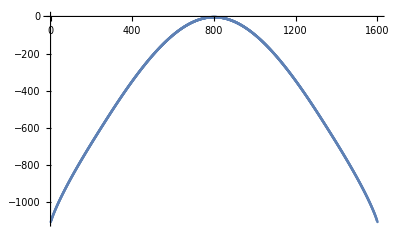

```mathematica
ListPlot[Log[coef] - n m Log[2]]
```

```mathematica
s=OpenWrite["2DIsing_DOS_L40.txt"];
For[i= 1, i≤Length@coef,i++ ,Write[s,N@(Log[coef] - n m Log[2])[[i]]]]
Close[s]
```

2DIsing_DOS_L40.txt